```mathematica
(*s=InputString["Enter xml file name","tooth.xml"]//StringReplace[#," "->""]&;*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_strong_red.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_weak_red.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_green_1000.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_red_1000.xml"];*)
xml=Import[NotebookDirectory[]<>"~images\\"<>"vorts1.xml"];
{tfifile,volumefile,legends,face,imagefilenames,txtfilenames,{featurefilename,visibilityfilename},resultxml,imagefile,rawfile,dataname,plotpath,imagepath}=xml;
(*Column[xml,Background->{{Lighter@LightYellow,Lighter@LightBlue}},Frame->True,FrameStyle->Directive[LightGray,Thin,Dashed]]*)

tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;

d = Import[volumefile,"Image3D"];
colorized=Image3D[d,ColorFunction->rgbafunction];
{lightness,chroma,hue,opacity}=ImageApply[List@@rgbafunction[#]&,d]//Image3D[#,ColorSpace->"RGB"]&//ColorSeparate[ColorConvert[#,"LCH"]]&;
(*lo=ImageMultiply[lightness,opacity];
co=ImageMultiply[chroma,opacity];*)
(*g1=ImageDifference[GaussianFilter[lightness,{2,Sqrt[2]/8.*2}],GaussianFilter[lightness,{4,Sqrt[2]/8.*4}]]
g2=ImageDifference[GaussianFilter[chroma,{2,Sqrt[2]/8.*2}],GaussianFilter[chroma,{4,Sqrt[2]/8.*4}]]
g3=ImageDifference[GaussianFilter[hue,{2,Sqrt[2]/8.*2}],GaussianFilter[hue,{4,Sqrt[2]/8.*4}]];
g4=ImageDifference[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]];*)
{g1,g2}=ParallelMap[ImageDifference[GaussianFilter[#,{2,Sqrt[2]/8.*2}],GaussianFilter[#,{4,Sqrt[2]/8.*4}]]&,{lightness,chroma}];

pos=intensity[[#]]&/@Flatten@Position[alpha,_?(#==0&)];
index=Flatten@Position[alpha,_?(#>0&)];
features=Table[ImageApply[If[#≥pos[[i]] && #≤pos[[i+1]],1,0]&,d],{i,1,Length[pos],2}];
chartcolors=rgbcolors[[#]]&/@index;
colorizedfeatures=ImageMultiply[colorized,#]&/@features;
viewpoints=<|"top":>Top,"back":>Back,"left":>Left,"bottom":>Bottom,"front":>Front,"right":>Right|>;
MapIndexed[Export[StringReplace[imagefile,"."->"_"<>ToString[First[#2]]<>"."],Show[#,Boxed->False,ViewPoint->viewpoints[face]]]&,colorizedfeatures];

intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
(*fun=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];*)
(*Plot[fun[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
index0=Flatten@Position[alpha0,_?(#>0&)];

targets=<|2->{0.2,0.8},3->{0.4,0.3,0.3},4->{0.1,0.2,0.3,0.4}|>;
target=targets[Length[index0]]
CloseKernels[];
LaunchKernels[8];
Clear[f];
Clear[data];
records={};
epsilon=0.01;
stepsize=0.05;
```

{0.4,0.3,0.3}

```mathematica
top:=Module[{list,count,img,list2,list3,d1},(* top *)
list=Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d1=Image3D[list3]]
back:=Module[{list,count,img,list2,list3,tmp,d2},(* back *)
list=Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left:=Module[{list,count,img,list2,list3,tmp,d3},(* left *)
list=Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom:=Module[{list,count,img,list2,list3,d4},(* bottom *)
list=Reverse@Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d4=Image3D[Reverse[list3]]]
front:=Module[{list,count,img,list2,list3,tmp,d5},(* front *)
list=Reverse@Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right:=Module[{list,count,img,list2,list3,tmp,d6},(* right *)
list=Reverse@Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices=<|"top":>top,"back":>back,"left":>left,"bottom":>bottom,"front":>front,"right":>right|>;
```

```mathematica
top2:=Module[{list,img,list2,list3,df,d1},(* top *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d1=Image3D[list3]
]
back2:=Module[{list,img,list2,list3,tmp,df,d2},(* back *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left2:=Module[{list,img,list2,list3,tmp,df,d3},(* left *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom2:=Module[{list,img,list2,list3,df,d4},(* bottom *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d4=Image3D[Reverse[list3]]]
front2:=Module[{list,img,list2,list3,tmp,df,d5},(* front *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right2:=Module[{list,img,list2,list3,tmp,df,d6},(* right *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices2=<|"top":>top2,"back":>back2,"left":>left2,"bottom":>bottom2,"front":>front2,"right":>right2|>;
```

```mathematica
VisibilitySaliency[peaks_]:=Module[{alpha2,fun,vis,viss,vs,mean,total},
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
Visibility[fun_]:=Module[{vis,viss,vs,mean,total},
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
```

```mathematica
(* x(k+1)=x(k)-(f-f0)/(f'-f0') *)
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
iteration=0;
previous={0,{0,0,0},{0,0,0}};
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,gradient,direction,square},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
gradient:=2*(mean-target);
square:=(mean-target)^2;
steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,g0,s0,dy,dx},
{rms0,mean0,p0,g0,s0}=previous;
dy=square-s0;
dx=gradient-g0;
If[Product[i,{i,dx}]≠0,direction=Normalize[dy/dx]*Norm[gradient];-direction*stepsize,-gradient*stepsize]
]];
previous={rms,mean,peaks,gradient,square};
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps,gradient,direction}
],{iterator,50}];
```

-3.653764641975725×10^9

0

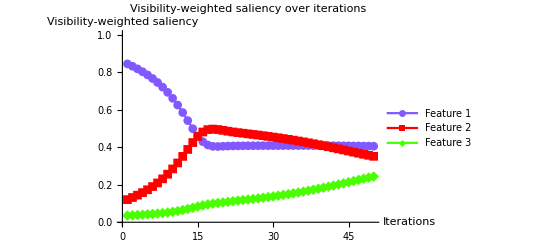

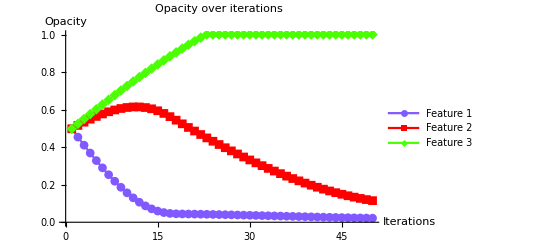

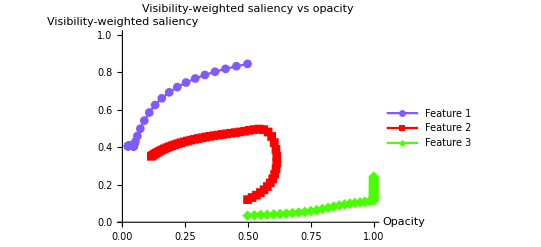

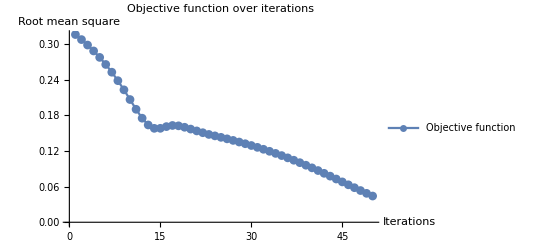

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps |  | 
1 | 0.843843
0.120606
0.0355513 | 0.498039
0.498039
0.498039 | 0.315759 | -0.0443843
0.0179394
0.0264449 | 0.887685
-0.358788
-0.528897 | direction$741640
2 | 0.831098
0.131845
0.0370572 | 0.453655
0.515979
0.524484 | 0.307279 | -0.043153
0.0171415
0.0260115 | 0.862196
-0.33631
-0.525886 | 0.863059
-0.342829
-0.52023
3 | 0.81716
0.144226
0.0386142 | 0.410502
0.53312
0.550496 | 0.298111 | -0.0417725
0.0159519
0.0258206 | 0.83432
-0.311549
-0.522772 | 0.83545
-0.319038
-0.516412
4 | 0.801834
0.1579
0.0402665 | 0.368729
0.549072
0.576316 | 0.288169 | -0.0402578
0.0146421
0.0256157 | 0.803668
-0.284201
-0.519467 | 0.805156
-0.292842
-0.512314
5 | 0.784831
0.173113
0.0420559 | 0.328472
0.563714
0.601932 | 0.277327 | -0.0385825
0.0131927
0.0253899 | 0.769662
-0.253774
-0.515888 | 0.771651
-0.263854
-0.507797
6 | 0.765804
0.190161
0.0440341 | 0.289889
0.576907
0.627322 | 0.265453 | -0.0367156
0.0115789
0.0251367 | 0.731609
-0.219677
-0.511932 | 0.734312
-0.231578
-0.502734
7 | 0.744337
0.209395
0.0462681 | 0.253174
0.588486
0.652458 | 0.252426 | -0.034621
0.00977208
0.0248489 | 0.688674
-0.18121
-0.507464 | 0.692419
-0.195442
-0.496978
8 | 0.719948
0.231211
0.0488413 | 0.218553
0.598258
0.677307 | 0.238173 | -0.0322598
0.0077407
0.0245191 | 0.639896
-0.137579
-0.502317 | 0.645195
-0.154814
-0.490381
9 | 0.692115
0.256027
0.0518581 | 0.186293
0.605998
0.701826 | 0.22274 | -0.0295943
0.00545227
0.0241421 | 0.58423
-0.0879463
-0.496284 | 0.591887
-0.109045
-0.482841
10 | 0.660351
0.28421
0.0554395 | 0.156699
0.611451
0.725968 | 0.206431 | -0.0265981
0.00287728
0.0237208 | 0.520702
-0.0315809
-0.489121 | 0.531963
-0.0575457
-0.474417
11 | 0.624371
0.31592
0.0597092 | 0.1301
0.614328
0.749689 | 0.190031 | -0.0232709
-6.20776×10^-6
0.0232771 | 0.448742
0.0318395
-0.480582 | 0.465417
0.000124155
-0.465541
12 | 0.584387
0.35085
0.064763 | 0.10683
0.614322
0.772966 | 0.175043 | -0.0196522
-0.00321017
0.0228624 | 0.368773
0.101701
-0.470474 | 0.393045
0.0642034
-0.457248
13 | 0.541541
0.38785
0.0706085 | 0.0871773
0.611112
0.795829 | 0.163679 | -0.0158152
-0.00673029
0.0225455 | 0.283082
0.175701
-0.458783 | 0.316305
0.134606
-0.450911
14 | 0.4984
0.424517
0.0770825 | 0.071362
0.604381
0.818374 | 0.157987 | -0.011845
-0.0104838
0.0223289 | 0.1968
0.249035
-0.445835 | 0.2369
0.209677
-0.446577
15 | 0.459234
0.457005
0.0837602 | 0.059517
0.593897
0.840703 | 0.158029 | -0.00791765
-0.0141403
0.022058 | 0.118469
0.314011
-0.43248 | 0.158353
0.282806
-0.441159
16 | 0.429204
0.480822
0.0899738 | 0.0515993
0.579757
0.862761 | 0.160894 | -0.00447253
-0.0170847
0.0215572 | 0.0584078
0.361645
-0.420052 | 0.0894506
0.341694
-0.431145
17 | 0.411428
0.493435
0.0951371 | 0.0471268
0.562672
0.884318 | 0.162805 | -0.00204517
-0.0188381
0.0208832 | 0.0228553
0.38687
-0.409726 | 0.0409034
0.376761
-0.417665
18 | 0.404394
0.496418
0.0991875 | 0.0450816
0.543834
0.905202 | 0.162198 | -0.000789722
-0.0194585
0.0202483 | 0.00878893
0.392836
-0.401625 | 0.0157944
0.389171
-0.404965
19 | 0.403542
0.493915
0.102543 | 0.0442919
0.524376
0.92545 | 0.159797 | -0.000393845
-0.0193711
0.0197649 | 0.00708326
0.38783
-0.394913 | 0.00787691
0.387422
-0.395299
20 | 0.404775
0.489537
0.105687 | 0.0438981
0.505005
0.945215 | 0.156743 | -0.000411837
-0.0189877
0.0193996 | 0.00955064
0.379075
-0.388626 | 0.00823675
0.379755
-0.387992
21 | 0.405997
0.4851
0.108904 | 0.0434862
0.486017
0.964614 | 0.15364 | -0.000533221
-0.0185447
0.0190779 | 0.0119935
0.370199
-0.382193 | 0.0106644
0.370894
-0.381558
22 | 0.406654
0.48106
0.112286 | 0.042953
0.467472
0.983692 | 0.150625 | -0.000626293
-0.0181266
0.0187529 | 0.013309
0.36212
-0.375428 | 0.0125259
0.362532
-0.375058
23 | 0.406928
0.477363
0.115709 | 0.0423267
0.449346
1. | 0.147726 | -0.000672526
-0.017747
0.0184195 | 0.0138561
0.354725
-0.368581 | 0.0134505
0.354939
-0.36839
24 | 0.407348
0.474191
0.118461 | 0.0416542
0.431599
1. | 0.145319 | -0.000707963
-0.0174333
0.0181413 | 0.0146969
0.348381
-0.363078 | 0.0141593
0.348666
-0.362826
25 | 0.407653
0.471003
0.121344 | 0.0409462
0.414165
1. | 0.14285 | -0.000743657
-0.0171118
0.0178555 | 0.0153064
0.342005
-0.357312 | 0.0148731
0.342236
-0.357109
26 | 0.407832
0.467799
0.12437 | 0.0402026
0.397054
1. | 0.140314 | -0.000767301
-0.0167883
0.0175556 | 0.015663
0.335597
-0.35126 | 0.015346
0.335767
-0.351113
27 | 0.407946
0.464517
0.127537 | 0.0394353
0.380265
1. | 0.137686 | -0.000781426
-0.0164587
0.0172402 | 0.0158922
0.329034
-0.344926 | 0.0156285
0.329175
-0.344804
28 | 0.408044
0.46111
0.130846 | 0.0386539
0.363807
1. | 0.13495 | -0.000791501
-0.0161179
0.0169094 | 0.0160888
0.32222
-0.338309 | 0.01583
0.322358
-0.338188
29 | 0.408147
0.457554
0.1343 | 0.0378624
0.347689
1. | 0.132093 | -0.000800899
-0.0157628
0.0165637 | 0.0162935
0.315107
-0.331401 | 0.016018
0.315255
-0.331273
30 | 0.408251
0.453842
0.137907 | 0.0370615
0.331926
1. | 0.129112 | -0.000810512
-0.015392
0.0162025 | 0.0165014
0.307684
-0.324185 | 0.0162102
0.307841
-0.324051
31 | 0.408347
0.449974
0.141679 | 0.0362509
0.316534
1. | 0.125999 | -0.000819774
-0.0150055
0.0158253 | 0.0166946
0.299948
-0.316643 | 0.0163955
0.30011
-0.316505
32 | 0.40843
0.445948
0.145621 | 0.0354312
0.301528
1. | 0.122753 | -0.000827922
-0.014603
0.0154309 | 0.0168602
0.291897
-0.308757 | 0.0165584
0.29206
-0.308619
33 | 0.408495
0.44176
0.149745 | 0.0346032
0.286925
1. | 0.119366 | -0.000834432
-0.0141842
0.0150186 | 0.0169905
0.28352
-0.300511 | 0.0166886
0.283684
-0.300373
34 | 0.40854
0.437406
0.154054 | 0.0337688
0.272741
1. | 0.115835 | -0.000838966
-0.0137488
0.0145877 | 0.0170795
0.274812
-0.291891 | 0.0167793
0.274975
-0.291755
35 | 0.408563
0.432881
0.158556 | 0.0329298
0.258992
1. | 0.112156 | -0.000841318
-0.0132963
0.0141376 | 0.0171251
0.265762
-0.282887 | 0.0168264
0.265925
-0.282752
36 | 0.40856
0.428185
0.163255 | 0.0320885
0.245696
1. | 0.108327 | -0.000841265
-0.0128266
0.0136679 | 0.0171202
0.256371
-0.273491 | 0.0168253
0.256532
-0.273358
37 | 0.408531
0.423318
0.168151 | 0.0312473
0.232869
1. | 0.104346 | -0.000838562
-0.0123398
0.0131784 | 0.0170621
0.246637
-0.263699 | 0.0167712
0.246796
-0.263568
38 | 0.408473
0.418282
0.173245 | 0.0304087
0.22053
1. | 0.100215 | -0.000833042
-0.011836
0.0126691 | 0.0169464
0.236563
-0.25351 | 0.0166608
0.236721
-0.253382
39 | 0.408381
0.413085
0.178533 | 0.0295757
0.208694
1. | 0.0959386 | -0.00082436
-0.0113161
0.0121405 | 0.0167629
0.22617
-0.242933 | 0.0164872
0.226323
-0.24281
40 | 0.408256
0.407736
0.184008 | 0.0287513
0.197377
1. | 0.0915229 | -0.00081227
-0.010781
0.0115933 | 0.0165117
0.215472
-0.231984 | 0.0162454
0.21562
-0.231865
41 | 0.408094
0.402249
0.189657 | 0.027939
0.186596
1. | 0.0869787 | -0.000796679
-0.010232
0.0110286 | 0.0161879
0.204498
-0.220686 | 0.0159336
0.204639
-0.220573
42 | 0.407896
0.396642
0.195463 | 0.0271424
0.176365
1. | 0.0823206 | -0.000777477
-0.00967092
0.0104484 | 0.015791
0.193284
-0.209075 | 0.0155495
0.193418
-0.208968
43 | 0.407658
0.390939
0.201403 | 0.0263649
0.166694
1. | 0.0775672 | -0.000754572
-0.00910021
0.00985479 | 0.0153167
0.181878
-0.197195 | 0.0150914
0.182004
-0.197096
44 | 0.407384
0.385169
0.207447 | 0.0256103
0.157593
1. | 0.0727424 | -0.000727992
-0.00852276
0.00925075 | 0.0147687
0.170338
-0.185107 | 0.0145598
0.170455
-0.185015
45 | 0.407076
0.379364
0.213561 | 0.0248823
0.149071
1. | 0.0678736 | -0.000697966
-0.00794179
0.00863976 | 0.0141513
0.158728
-0.172879 | 0.0139593
0.158836
-0.172795
46 | 0.406735
0.373562
0.219703 | 0.0241843
0.141129
1. | 0.062993 | -0.000664784
-0.00736114
0.00802592 | 0.0134702
0.147124
-0.160594 | 0.0132957
0.147223
-0.160518
47 | 0.406364
0.367807
0.225829 | 0.0235196
0.133768
1. | 0.0581369 | -0.000628698
-0.00678509
0.00741379 | 0.012728
0.135614
-0.148342 | 0.012574
0.135702
-0.148276
48 | 0.405971
0.362142
0.231887 | 0.0228909
0.126983
1. | 0.0533437 | -0.000590242
-0.0062181
0.00680834 | 0.0119424
0.124284
-0.136226 | 0.0118048
0.124362
-0.136167
49 | 0.405559
0.356613
0.237828 | 0.0223006
0.120765
1. | 0.0486528 | -0.000550012
-0.00566465
0.00621466 | 0.0111187
0.113225
-0.124344 | 0.0110002
0.113293
-0.124293
50 | 0.405136
0.351266
0.243599 | 0.0217506
0.1151
1. | 0.0441046 | -0.000508543
-0.00512944
0.00563798 | 0.0102718
0.102531
-0.112803 | 0.0101709
0.102589
-0.11276

```mathematica
t2-t1
iteration
saliency5=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_newton.png",saliency5];
opacity5=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_newton.png",opacity5];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity5=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_newton.png",saliencyopacity5];
rmslist5=#3&@@@list;
rms5=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_newton.png",rms5];
table5=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_newton.png",table5];
path5=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path5]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,gradient},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
gradient=2*(mean-target);
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps,gradient}
],{iterator,100}];
```

-3.6537646776145556×10^9

0

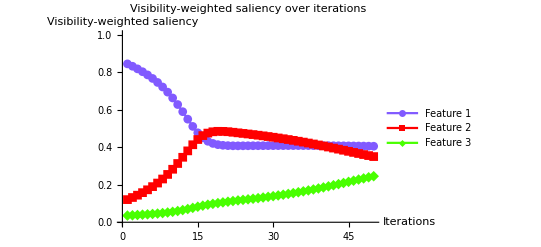

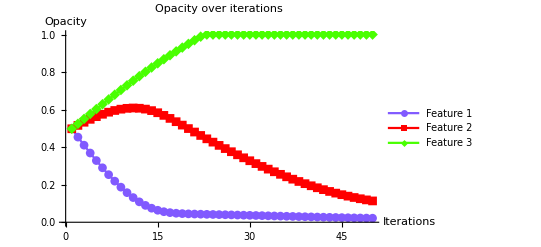

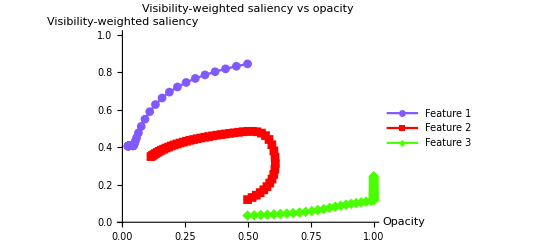

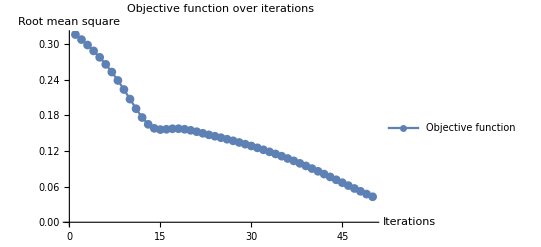

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | 
1 | 0.843843
0.120606
0.0355513 | 0.498039
0.498039
0.498039 | 0.315759 | -0.0443843
0.0179394
0.0264449 | 0.887685
-0.358788
-0.528897
2 | 0.831098
0.131845
0.0370572 | 0.453655
0.515979
0.524484 | 0.307279 | -0.0431098
0.0168155
0.0262943 | 0.862196
-0.33631
-0.525886
3 | 0.817209
0.144164
0.0386268 | 0.410545
0.532794
0.550778 | 0.298141 | -0.0417209
0.0155836
0.0261373 | 0.834418
-0.311672
-0.522746
4 | 0.801946
0.157761
0.0402934 | 0.368824
0.548378
0.576916 | 0.288236 | -0.0401946
0.0142239
0.0259707 | 0.803892
-0.284479
-0.519413
5 | 0.785027
0.172875
0.0420986 | 0.32863
0.562602
0.602886 | 0.27744 | -0.0385027
0.0127125
0.0257901 | 0.770053
-0.254251
-0.515803
6 | 0.766114
0.189791
0.0440951 | 0.290127
0.575314
0.628676 | 0.265627 | -0.0366114
0.0110209
0.0255905 | 0.732227
-0.220418
-0.51181
7 | 0.744809
0.208841
0.0463501 | 0.253516
0.586335
0.654267 | 0.25268 | -0.0344809
0.0091159
0.025365 | 0.689618
-0.182318
-0.5073
8 | 0.720663
0.23039
0.0489473 | 0.219035
0.595451
0.679632 | 0.238536 | -0.0320663
0.00696101
0.0251053 | 0.641326
-0.13922
-0.502105
9 | 0.693212
0.2548
0.0519883 | 0.186968
0.602412
0.704737 | 0.223253 | -0.0293212
0.00452002
0.0248012 | 0.586424
-0.0904004
-0.496023
10 | 0.662076
0.282336
0.055588 | 0.157647
0.606932
0.729538 | 0.20715 | -0.0262076
0.00176638
0.0244412 | 0.524152
-0.0353275
-0.488824
11 | 0.627164
0.312982
0.0598536 | 0.13144
0.608698
0.75398 | 0.190999 | -0.0227164
-0.00129822
0.0240146 | 0.454328
0.0259644
-0.480293
12 | 0.589015
0.346141
0.0648438 | 0.108723
0.6074
0.777994 | 0.176214 | -0.0189015
-0.00461414
0.0235156 | 0.37803
0.0922829
-0.470312
13 | 0.549211
0.380288
0.0705004 | 0.0898218
0.602786
0.80151 | 0.164702 | -0.0149211
-0.00802883
0.02295 | 0.298422
0.160577
-0.458999
14 | 0.510561
0.412852
0.0765868 | 0.0749007
0.594757
0.82446 | 0.15798 | -0.0110561
-0.0112852
0.0223413 | 0.221122
0.225704
-0.446826
15 | 0.476542
0.440755
0.0827037 | 0.0638445
0.583472
0.846801 | 0.155872 | -0.00765418
-0.0140755
0.0217296 | 0.153084
0.281509
-0.434593
16 | 0.449912
0.461651
0.0884375 | 0.0561904
0.569397
0.868531 | 0.156398 | -0.00499119
-0.0161651
0.0211563 | 0.0998237
0.323301
-0.423125
17 | 0.431446
0.475004
0.0935502 | 0.0511992
0.553231
0.889687 | 0.157307 | -0.00314463
-0.0175004
0.020645 | 0.0628926
0.350007
-0.4129
18 | 0.419962
0.481988
0.0980492 | 0.0480545
0.535731
0.910332 | 0.157377 | -0.00199624
-0.0181988
0.0201951 | 0.0399248
0.363977
-0.403902
19 | 0.413419
0.484489
0.102092 | 0.0460583
0.517532
0.930527 | 0.156401 | -0.00134191
-0.0184489
0.0197908 | 0.0268381
0.368979
-0.395817
20 | 0.409936
0.484201
0.105863 | 0.0447164
0.499083
0.950318 | 0.154615 | -0.000993572
-0.0184201
0.0194137 | 0.0198714
0.368402
-0.388273
21 | 0.408186
0.482302
0.109512 | 0.0437228
0.480663
0.969732 | 0.152301 | -0.000818587
-0.0182302
0.0190488 | 0.0163717
0.364604
-0.380976
22 | 0.407361
0.479502
0.113137 | 0.0429042
0.462433
0.98878 | 0.149658 | -0.000736142
-0.0179502
0.0186863 | 0.0147228
0.359004
-0.373726
23 | 0.407165
0.476409
0.116426 | 0.0421681
0.444483
1. | 0.14705 | -0.000716511
-0.0176409
0.0183574 | 0.0143302
0.352818
-0.367148
24 | 0.407366
0.473391
0.119243 | 0.0414516
0.426842
1. | 0.144674 | -0.00073657
-0.0173391
0.0180757 | 0.0147314
0.346782
-0.361513
25 | 0.407529
0.470287
0.122183 | 0.040715
0.409503
1. | 0.142213 | -0.000752938
-0.0170287
0.0177817 | 0.0150588
0.340575
-0.355633
26 | 0.407672
0.467076
0.125252 | 0.0399621
0.392474
1. | 0.139654 | -0.000767232
-0.0167076
0.0174748 | 0.0153446
0.334152
-0.349496
27 | 0.407802
0.463742
0.128455 | 0.0391948
0.375767
1. | 0.136992 | -0.000780231
-0.0163742
0.0171545 | 0.0156046
0.327485
-0.343089
28 | 0.407923
0.460276
0.1318 | 0.0384146
0.359392
1. | 0.134217 | -0.000792336
-0.0160276
0.01682 | 0.0158467
0.320552
-0.336399
29 | 0.408035
0.456669
0.135296 | 0.0376223
0.343365
1. | 0.131323 | -0.000803532
-0.0156669
0.0164704 | 0.0160706
0.313338
-0.329409
30 | 0.408136
0.452915
0.138949 | 0.0368187
0.327698
1. | 0.128305 | -0.000813563
-0.0152915
0.0161051 | 0.0162713
0.30583
-0.322101
31 | 0.408224
0.449007
0.142769 | 0.0360052
0.312406
1. | 0.125156 | -0.000822374
-0.0149007
0.0157231 | 0.0164475
0.298014
-0.314461
32 | 0.408298
0.444938
0.146764 | 0.0351828
0.297506
1. | 0.121871 | -0.000829843
-0.0144938
0.0153236 | 0.0165969
0.289876
-0.306473
33 | 0.408355
0.440705
0.15094 | 0.034353
0.283012
1. | 0.118443 | -0.000835527
-0.0140705
0.014906 | 0.0167105
0.28141
-0.29812
34 | 0.408394
0.436302
0.155304 | 0.0335174
0.268941
1. | 0.114871 | -0.000839407
-0.0136302
0.0144696 | 0.0167881
0.272604
-0.289392
35 | 0.40841
0.431729
0.159861 | 0.032678
0.255311
1. | 0.111148 | -0.000841005
-0.0131729
0.0140139 | 0.0168201
0.263457
-0.280277
36 | 0.408402
0.426982
0.164616 | 0.031837
0.242138
1. | 0.107275 | -0.000840242
-0.0126982
0.0135384 | 0.0168048
0.253964
-0.270769
37 | 0.408367
0.422064
0.169569 | 0.0309968
0.22944
1. | 0.10325 | -0.000836668
-0.0122064
0.0130431 | 0.0167334
0.244129
-0.260862
38 | 0.408302
0.41698
0.174719 | 0.0301601
0.217234
1. | 0.0990766 | -0.000830165
-0.011698
0.0125281 | 0.0166033
0.233959
-0.250563
39 | 0.408205
0.411734
0.180061 | 0.0293299
0.205536
1. | 0.0947579 | -0.000820487
-0.0111734
0.0119939 | 0.0164097
0.223468
-0.239878
40 | 0.408074
0.40634
0.185586 | 0.0285095
0.194362
1. | 0.0903031 | -0.000807416
-0.010634
0.0114414 | 0.0161483
0.21268
-0.228828
41 | 0.407907
0.400812
0.191281 | 0.027702
0.183728
1. | 0.0857231 | -0.000790723
-0.0100812
0.0108719 | 0.0158145
0.201623
-0.217438
42 | 0.407704
0.395169
0.197127 | 0.0269113
0.173647
1. | 0.0810338 | -0.000770426
-0.00951691
0.0102873 | 0.0154085
0.190338
-0.205747
43 | 0.407465
0.389437
0.203099 | 0.0261409
0.16413
1. | 0.076255 | -0.00074647
-0.00894366
0.00969013 | 0.0149294
0.178873
-0.193803
44 | 0.407189
0.383645
0.209166 | 0.0253944
0.155187
1. | 0.071412 | -0.000718895
-0.00836452
0.00908341 | 0.0143779
0.16729
-0.181668
45 | 0.40688
0.377829
0.215291 | 0.0246755
0.146822
1. | 0.0665341 | -0.000688009
-0.00778291
0.00847092 | 0.0137602
0.155658
-0.169418
46 | 0.40654
0.372028
0.221432 | 0.0239875
0.139039
1. | 0.0616543 | -0.00065398
-0.00720281
0.00785679 | 0.0130796
0.144056
-0.157136
47 | 0.406173
0.366285
0.227542 | 0.0233335
0.131836
1. | 0.0568093 | -0.000617293
-0.00662848
0.00724577 | 0.0123459
0.13257
-0.144915
48 | 0.405781
0.360646
0.233573 | 0.0227162
0.125208
1. | 0.0520385 | -0.000578118
-0.00606463
0.00664275 | 0.0115624
0.121293
-0.132855
49 | 0.405377
0.355154
0.239469 | 0.0221381
0.119143
1. | 0.0473812 | -0.000537697
-0.00551542
0.00605312 | 0.0107539
0.110308
-0.121062
50 | 0.404961
0.349857
0.245182 | 0.0216004
0.113628
1. | 0.0428774 | -0.000496073
-0.00498574
0.00548182 | 0.00992146
0.0997149
-0.109636

```mathematica
t2-t1
iteration
saliency1=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_fixed.png",saliency1];
opacity1=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_fixed.png",opacity1];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity1=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_fixed.png",saliencyopacity1];
rmslist1=#3&@@@list;
rms1=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_fixed.png",rms1];
table1=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_fixed.png",table1];
path1=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path1]}];
```

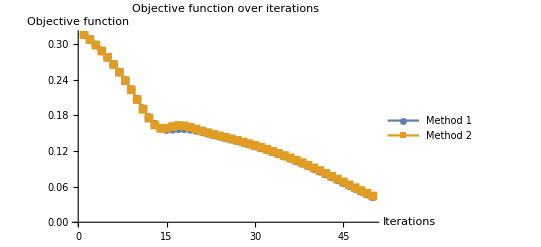

```mathematica
rmslists1=ListLinePlot[{rmslist1,rmslist5},PlotLegends->{"Method 1","Method 2"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Objective function"}]
Export[plotpath<>dataname<>"_rms_fixed_newton.png",rmslists1];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*parallel gradient*)
multipliers={1,2,4,8};
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,meanlist,peaklist,rmslist,minindex},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=ParallelMap[Clip[peaks+steps*#,{0,1}]&,multipliers];
meanlist=ParallelMap[VisibilitySaliency[#]&,peaklist];
rmslist=ParallelMap[RootMeanSquare[#-target]&,meanlist];
minindex=First@Ordering[rmslist,1];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=meanlist[[minindex]];
If[t2==0 && rmslist[[minindex]]<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,20}];
```

19.202717

18

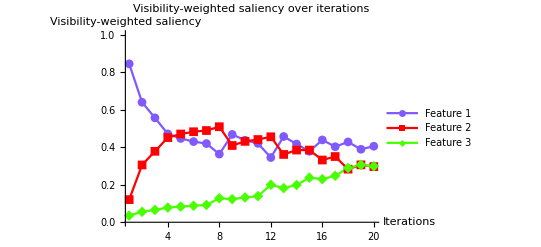

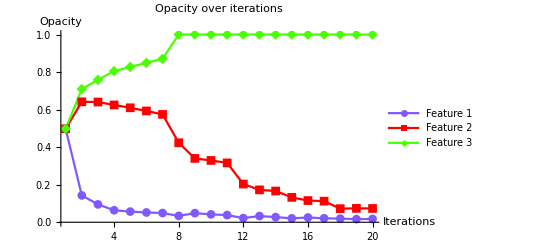

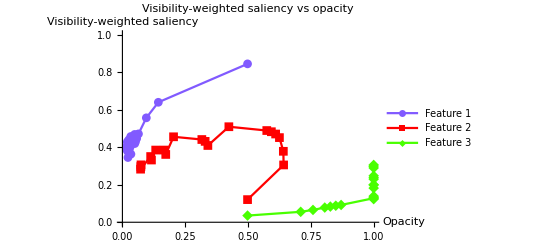

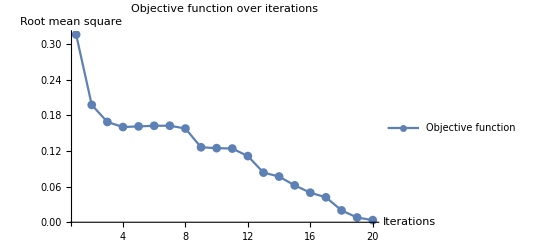

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.843843
0.120606
0.0355513 | 0.498039
0.498039
0.498039 | 0.315759 | -0.0443843
0.0179394
0.0264449 | 8
2 | 0.639102
0.30531
0.0555883 | 0.142965
0.641554
0.709598 | 0.197429 | -0.0239102
-0.000530969
0.0244412 | 2
3 | 0.556342
0.377969
0.0656888 | 0.0951447
0.640492
0.75848 | 0.168744 | -0.0156342
-0.00779689
0.0234311 | 2
4 | 0.470762
0.450979
0.0782595 | 0.0638762
0.624899
0.805343 | 0.160178 | -0.00707616
-0.0150979
0.0221741 | 1
5 | 0.446492
0.470095
0.0834135 | 0.0568001
0.609801
0.827517 | 0.161249 | -0.00464919
-0.0170095
0.0216586 | 1
6 | 0.429715
0.482235
0.0880496 | 0.0521509
0.592791
0.849175 | 0.162292 | -0.00297151
-0.0182235
0.021195 | 1
7 | 0.419199
0.488612
0.0921887 | 0.0491794
0.574568
0.87037 | 0.162408 | -0.00191991
-0.0188612
0.0207811 | 8
8 | 0.363004
0.508904
0.128092 | 0.03382
0.423678
1. | 0.157651 | 0.00369956
-0.0208904
0.0171908 | 4
9 | 0.46783
0.40897
0.123201 | 0.0486183
0.340117
1. | 0.126139 | -0.00678298
-0.010897
0.0176799 | 1
10 | 0.436843
0.430904
0.132252 | 0.0418353
0.32922
1. | 0.124677 | -0.00368434
-0.0130904
0.0167748 | 1
11 | 0.42015
0.440747
0.139103 | 0.038151
0.316129
1. | 0.123967 | -0.00201495
-0.0140747
0.0160897 | 8
12 | 0.344806
0.455275
0.199919 | 0.0220313
0.203532
1. | 0.111315 | 0.00551939
-0.0155275
0.0100081 | 2
13 | 0.456853
0.361236
0.181912 | 0.0330701
0.172477
1. | 0.0835203 | -0.00568527
-0.00612356
0.0118088 | 1
14 | 0.416736
0.384653
0.198612 | 0.0273848
0.166353
1. | 0.0768674 | -0.00167357
-0.00846527
0.0101388 | 4
15 | 0.377849
0.384604
0.237547 | 0.0206906
0.132492
1. | 0.0620452 | 0.0022151
-0.00846037
0.00624527 | 2
16 | 0.438659
0.33156
0.22978 | 0.0251208
0.115571
1. | 0.0497372 | -0.00386594
-0.00315602
0.00702196 | 1
17 | 0.402394
0.350124
0.247482 | 0.0212548
0.112415
1. | 0.0419376 | -0.000239395
-0.0050124
0.00525179 | 8
18 | 0.427967
0.282798
0.289235 | 0.0193397
0.072316
1. | 0.0199496 | -0.00279671
0.0017202
0.00107652 | 1
19 | 0.388776
0.305814
0.30541 | 0.0165429
0.0740362
1. | 0.00793828 | 0.0011224
-0.000581432
-0.000540967 | 1
20 | 0.404952
0.296539
0.298508 | 0.0176653
0.0734548
0.999459 | 0.00359275 | -0.00049521
0.000346058
0.000149153 | 1

```mathematica
t2-t1
iteration
saliency2=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_parallelsearch.png",saliency2];
opacity2=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_parallelsearch.png",opacity2];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity2=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_parallelsearch.png",saliencyopacity2];
rmslist2=#3&@@@list;
rms2=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_parallelsearch.png",rms2];
table2=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_parallelsearch.png",table2];
path2=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path2]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*line search*)
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaklist,minindex,minrms,minmean,rms2,mean2},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=Map[Clip[peaks+steps*#,{0,1}]&,multipliers];
minindex=1;
minmean=VisibilitySaliency[peaklist[[minindex]]];
minrms=RootMeanSquare[minmean-target];
Do[mean2=VisibilitySaliency[peaklist[[i]]];
rms2=RootMeanSquare[mean2-target];
If[rms2<minrms,minrms=rms2;minmean=mean2;minindex=i,Return[i]];
,{i,Range[2,4]}];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=minmean;
If[t2==0 && minrms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,20}];
```

```mathematica
t2-t1
iteration
saliency3=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_linesearch.png",saliency3];
opacity3=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_linesearch.png",opacity3];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity3=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_linesearch.png",saliencyopacity3];
rmslist3=#3&@@@list;
rms3=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_linesearch.png",rms3];
table3=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_linesearch.png",table3];
path3=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path3]}];
```

34.845697

18

-Graphics-

-Graphics-

-Graphics-

-Graphics-

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.843843
0.120606
0.0355513 | 0.498039
0.498039
0.498039 | 0.315759 | -0.0443843
0.0179394
0.0264449 | 8
2 | 0.639102
0.30531
0.0555883 | 0.142965
0.641554
0.709598 | 0.197429 | -0.0239102
-0.000530969
0.0244412 | 2
3 | 0.556342
0.377969
0.0656888 | 0.0951447
0.640492
0.75848 | 0.168744 | -0.0156342
-0.00779689
0.0234311 | 2
4 | 0.470762
0.450979
0.0782595 | 0.0638762
0.624899
0.805343 | 0.160178 | -0.00707616
-0.0150979
0.0221741 | 1
5 | 0.446492
0.470095
0.0834135 | 0.0568001
0.609801
0.827517 | 0.161249 | -0.00464919
-0.0170095
0.0216586 | 1
6 | 0.429715
0.482235
0.0880496 | 0.0521509
0.592791
0.849175 | 0.162292 | -0.00297151
-0.0182235
0.021195 | 1
7 | 0.419199
0.488612
0.0921887 | 0.0491794
0.574568
0.87037 | 0.162408 | -0.00191991
-0.0188612
0.0207811 | 8
8 | 0.363004
0.508904
0.128092 | 0.03382
0.423678
1. | 0.157651 | 0.00369956
-0.0208904
0.0171908 | 4
9 | 0.46783
0.40897
0.123201 | 0.0486183
0.340117
1. | 0.126139 | -0.00678298
-0.010897
0.0176799 | 1
10 | 0.436843
0.430904
0.132252 | 0.0418353
0.32922
1. | 0.124677 | -0.00368434
-0.0130904
0.0167748 | 1
11 | 0.42015
0.440747
0.139103 | 0.038151
0.316129
1. | 0.123967 | -0.00201495
-0.0140747
0.0160897 | 8
12 | 0.344806
0.455275
0.199919 | 0.0220313
0.203532
1. | 0.111315 | 0.00551939
-0.0155275
0.0100081 | 2
13 | 0.456853
0.361236
0.181912 | 0.0330701
0.172477
1. | 0.0835203 | -0.00568527
-0.00612356
0.0118088 | 1
14 | 0.416736
0.384653
0.198612 | 0.0273848
0.166353
1. | 0.0768674 | -0.00167357
-0.00846527
0.0101388 | 4
15 | 0.377849
0.384604
0.237547 | 0.0206906
0.132492
1. | 0.0620452 | 0.0022151
-0.00846037
0.00624527 | 2
16 | 0.438659
0.33156
0.22978 | 0.0251208
0.115571
1. | 0.0497372 | -0.00386594
-0.00315602
0.00702196 | 1
17 | 0.402394
0.350124
0.247482 | 0.0212548
0.112415
1. | 0.0419376 | -0.000239395
-0.0050124
0.00525179 | 8
18 | 0.427967
0.282798
0.289235 | 0.0193397
0.072316
1. | 0.0199496 | -0.00279671
0.0017202
0.00107652 | 1
19 | 0.388776
0.305814
0.30541 | 0.0165429
0.0740362
1. | 0.00793828 | 0.0011224
-0.000581432
-0.000540967 | 1
20 | 0.404952
0.296539
0.298508 | 0.0176653
0.0734548
0.999459 | 0.00359275 | -0.00049521
0.000346058
0.000149153 | 1

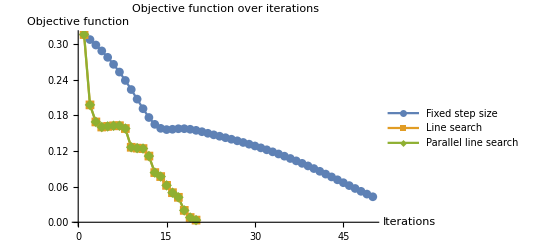

```mathematica
rmslists2=ListLinePlot[{rmslist1,rmslist2,rmslist3},PlotLegends->{"Fixed step size","Line search","Parallel line search"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Objective function"}]
Export[plotpath<>dataname<>"_rms_fixed_linesearch_parallel.png",rmslists2];
```

```mathematica
(*(* compare the performance of 3 methods for computing visibility-weighted saliency *)
n=10;

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ParallelMap[ImageMultiply[#,vis]&,{g1,g2}];
total=ParallelMap[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=ParallelTable[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ImageMultiply[g1,vis];(* weighted by lightness DoG (difference of Gaussians) *)
(*vs=Table[ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,features}];*)
total=ImageMeasurements[viss,"TotalIntensity"];
vs=ParallelTable[If[total≠0,ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/total,0],{i,features}];
viss2=ImageMultiply[g2,vis];(* weighted by chroma DoG *)
(*vs2=Table[ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,features}];*)
total2=ImageMeasurements[viss2,"TotalIntensity"];
vs2=ParallelTable[If[total2≠0,ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/total2,0],{i,features}];
mean=Mean[{vs,vs2}]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n*)
```

```mathematica
(*(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
iteration=0;
previous={0,{0,0,0},{0,0,0}};
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,gradient},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
gradient:=2*(mean-target);
(*steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,dy,dx},
{rms0,mean0,p0}=previous;
dy=Table[RootMeanSquare[Table[If[i==n,mean0[[i]],mean[[i]]],{i,Length[mean]}]-target],{n,Length[mean]}];
dx=peaks-p0;
If[Product[i,{i,dx}]≠0,-dy/dx*stepsize,-gradient*stepsize]
]];*)
steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,dy,dx},
{rms0,mean0,p0}=previous;
dy=mean-mean0;
dx=peaks-p0;
If[Product[i,{i,dx}]≠0,-dy/dx*gradient*stepsize,-gradient*stepsize]
]];
previous={rms,mean,peaks};
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps}
],{iterator,10}];*)
```

```mathematica
(*t2-t1
iteration
saliency4=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_difference.png",saliency4];
opacity4=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_difference.png",opacity4];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity4=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_difference.png",saliencyopacity4];
rms4=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_difference.png",rms4];
table4=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_difference.png",table4];
path4=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path4]}];*)
```

```mathematica
recordxml=plotpath<>"records.xml";
recordmap=If[FileExistsQ[recordxml],Association@Import[recordxml],<||>];
AssociateTo[recordmap,dataname->records];
Export[recordxml,Normal[recordmap]];
dataname->records
```

{vorts1}→{{-3.653764641975725×10^9,0,{0.0217506,0.1151,1.}},{-3.6537646776145556×10^9,0,{0.0216004,0.113628,1.}},{19.202717,18,{0.0176653,0.0734548,0.999459}},{34.845697,18,{0.0176653,0.0734548,0.999459}}}

```mathematica
ObjectiveFunction[pos_]:=RootMeanSquare[VisibilitySaliency[pos]-target];
```

```mathematica
(*ObjectiveFunction[{0.1,0.3,0.6}]
(*FindMinimum[{ObjectiveFunction[{x1,x2,x3}],0≤x1≤1,0≤x2≤1,0≤x3≤1},{{x1,{0.1}},{x2,{0.3}},{x3,{0.6}}}]*)
FindMinimum[x1 Cos[x1]+x2 Cos[x2],{{x1,0},{x2,0}}]
Plot3D[x1 Sin[x1]+x2 Sin[x2],{x1,0,10},{x2,0,10}]*)
```

```mathematica
(*range=Range[0,1,0.1];
coordinates=Flatten[Table[{i,j,k},{i,range},{j,range},{k,range}],2];
Length[coordinates]
AbsoluteTiming[
searchspace=ParallelTable[Module[{mean,rms},
mean=VisibilitySaliency[c];
rms=RootMeanSquare[mean-target];
{mean,c,rms}
],{c,coordinates}];
]*)
```

```mathematica
(*transform=RotationTransform[-90 Degree,{0,0,1}];
vec=transform[{1.3, -2.4, 2.}];
opacitylist=#2&@@@searchspace;
rmslist=#3&@@@searchspace;
merged=ParallelTable[Append[opacitylist[[i]],rmslist[[i]]],{i,Length[opacitylist]}];
densityplot=ListDensityPlot3D[merged,ColorFunction->"LightTemperatureMap",PlotLegends->Automatic,PlotLabel->{"x","y","z"},PlotTheme->"Detailed",OpacityFunction->Automatic];
paths={path1,path3};
pathcolors={Red,Green,Blue};
plotlegends={{"Fixed step size"},{"Adaptive step size with line search"},{"Adaptive step size with parallel search"}};
pointplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]],Thick,PointSize[Large]},PlotLegends->plotlegends[[i]]],{i,Length[paths]}];
lineplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]]}]/.Point->Line,{i,Length[paths]}];
sp=Show[densityplot,PlotLabel->"Objective function in parameter space",ViewPoint->vec]
sp2=Show[densityplot,pointplots[[1]],pointplots[[2]],lineplots[[1]],lineplots[[2]],PlotLabel->"Gradient descent in parameter space",ViewPoint->vec]
Export[plotpath<>dataname<>"_parameterspace.png",sp];
Export[plotpath<>dataname<>"_parameterspace_path.png",sp2];

{c1,c2,c3}=chartcolors;
blend1=Blend[{{0,Black},{0.5,c1},{1,White}},#]&;
blend2=Blend[{{0,Black},{0.5,c2},{1,White}},#]&;
blend3=Blend[{{0,Black},{0.5,c3},{1,White}},#]&;
saliencylist=#&@@@searchspace;
first=#&@@@saliencylist;
second=#2&@@@saliencylist;
third=#3&@@@saliencylist;
merged1=ParallelTable[Append[opacitylist[[i]],first[[i]]],{i,Length[opacitylist]}];
merged2=ParallelTable[Append[opacitylist[[i]],second[[i]]],{i,Length[opacitylist]}];
merged3=ParallelTable[Append[opacitylist[[i]],third[[i]]],{i,Length[opacitylist]}];
dplots=ListDensityPlot3D[#1,ColorFunction->#2,PlotLegends->Automatic,PlotTheme->"Detailed",OpacityFunction->(#&)]&@@@{{merged1,blend1},{merged2,blend2},{merged3,blend3}};
densityplots=MapIndexed[Show[#,PlotLabel->"Visibility-weighted saliency of feature "<>ToString[First@#2],ViewPoint->vec]&,dplots]
MapIndexed[Export[plotpath<>dataname<>"_densityplot"<>ToString[First@#2]<>".png",#]&,densityplots];*)
```

```mathematica
saveTransferFunction[peaks_,filename_]:=Module[{a2,rgba2,intensity2,rgbafunction2,rgba2denormalized,xrgba,strlist,alphaMode,gammaValue,domain,threshold,k,int,split,colorL,keylist,keys,TransFuncIntensity,VoreenData,xml},
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
a2=IntegerPart[255*alpha0[[#]]]&/@rangeOfAlpha;
rgba2=(#/255.&)/@Transpose[{r,g,b,a2}]//(RGBColor/@#&);
intensity2=intensity0[[#]]&/@rangeOfAlpha;
rgbafunction2=(Blend[Transpose[{intensity2,rgba2}], #] & );(* for return only. not used in this function *)

rgba2denormalized=Transpose[{r,g,b,a2}];
xrgba=Table[Join[{intensity2[[i]]},rgba2denormalized[[i]]],{i,Length[intensity2]}];
strlist={ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&@@@xrgba;
alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({int=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xml=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function exported from Mathematica"]},VoreenData,{}];
Export[filename,xml, "XML"];
rgbafunction2
];
```

```mathematica
tf1=saveTransferFunction[Last[path1],plotpath<>dataname<>"_optimized_fixed.tfi"];
tf2=saveTransferFunction[Last[path2],plotpath<>dataname<>"_optimized_parallelsearch.tfi"];
tf3=saveTransferFunction[Last[path3],plotpath<>dataname<>"_optimized_linesearch.tfi"];
Image3D[d,ColorFunction->rgbafunction,ViewPoint->viewpoints[face]]
Image3D[d,ColorFunction->tf3,ViewPoint->viewpoints[face]]
ListLinePlot[Transpose[{intensity,alpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"Before optimization"]
(*Transpose[{intensity,r,g,b,a}]*)
ListLinePlot[Transpose[{intensity0[[#]]&/@rangeOfAlpha,alpha0[[#]]&/@rangeOfAlpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"After optimization"]
(*xrgba*)
```

-Graphics-

-Graphics-